```mathematica
f[x_] := 63 * x^3 - 248 * x^2 + 155 * x + 66
Plot [f[x], {x, -1, 4}]
```

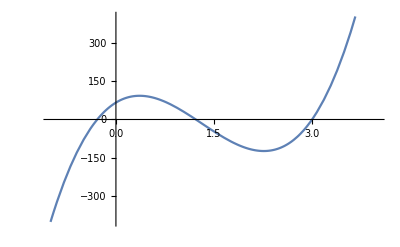

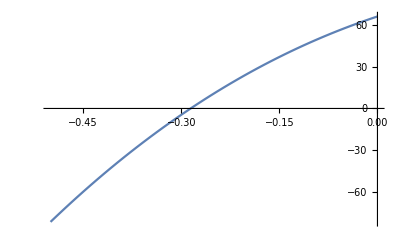

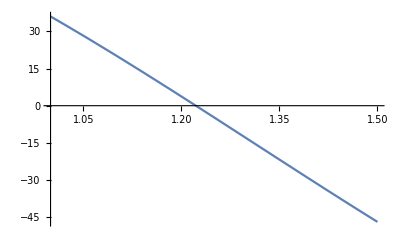

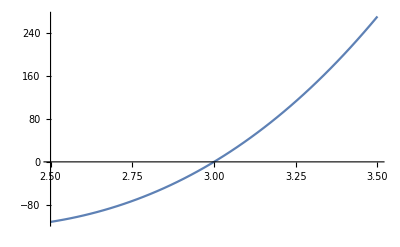

```mathematica
Plot[f[x], {x, -0.5, 0}]
Plot[f[x], {x, 1, 1.5}]
Plot[f[x], {x, 2.5,  3.5}]
```

```mathematica
func[x_]:=63*x^3-248*x^2+155*x+66;
constCoef = 1.5;
x1 = 1;
x2 = 1.5;
eps = 0.001;
iter = 0;
While[Abs[x2 -x1] > eps,
x2 = x1;
x1 = x2 -  func[x2]/(func[constCoef] - func[x2]) * (constCoef - x2);
Increment[iter];
Print["Итерация ", iter, ": x = ", x1]]
Print[ "Количество итераций = ", iter]
```

Итерация 1: x = 1.21719

Итерация 2: x = 1.22222

Итерация 3: x = 1.22222

Количество итераций = 3

{{x→1.22222}}

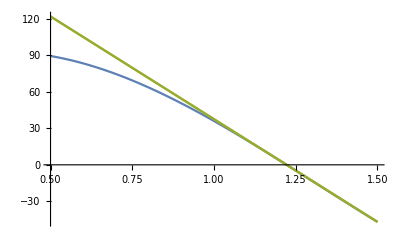

{{x→1.22222}}

```mathematica
func[x_]:=63*x^3-248*x^2+155*x+66;
constCoef = 1.5;
x1= 1;
x2 = x1;
x1 = x2 -  (func[x2]/(func[constCoef] - func[x2])) * (constCoef - x2);
FirstSec[x_] = ((x - x1) * (func[constCoef] - func[x1]))/(constCoef -x1) + func[x1];
Solve[FirstSec[x] == 0]
x2 = x1;
x1 = x2 -  (func[x2]/(func[constCoef] - func[x2])) * (constCoef - x2);
SecondSec[x_] = ((x - x1) * (func[constCoef] - func[x1]))/(constCoef -x1) + func[x1];

Plot[{func[x], FirstSec[x], SecondSec[x]}, {x, 0.5, 1.5}]
Solve[SecondSec[x] == 0]
```

```mathematica
(* Задание 2 *)
```

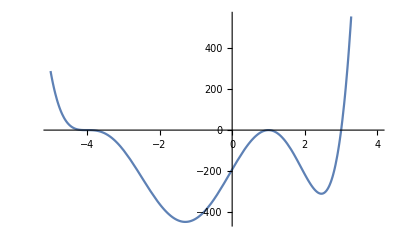

```mathematica
func2[x_] = x ^6 + 7 * x^5 - 5 * x^4 - 95 * x^3 - 20 * x^2 + 304 * x - 192; 
Plot[func2[x], {x, -5, 4}]
```

```mathematica
Solve[func2[x] == 0]
```

```mathematica
{{x->-4},{x->-4},{x->-4},{x->1},{x->1},{x->3}}
```

```mathematica
NSolve[func2[x] == 0]
```

{{x→-4.},{x→-4.},{x→-4.},{x→1.},{x→1.},{x→3.}}

```mathematica
Roots[func2[x] == 0, x]
```

x==-4||x==-4||x==-4||x==1||x==1||x==3

```mathematica
FindRoot[func2[x] == 0, {x, -4}]
FindRoot[func2[x] == 0, {x, 1}]
FindRoot[func2[x] == 0, {x, 3}]
```

{x→-4.}

{x→1.}

{x→3.}

```mathematica
Factor[func2[x]]
```

(-3+x) (-1+x)^2 (4+x)^3

-1+3 x-x^2+Log[x]/Log[2]

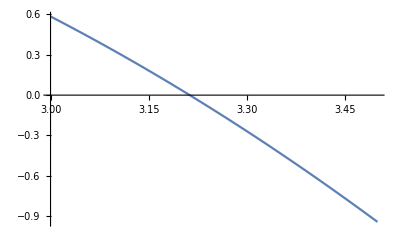

```mathematica
(* Задание 3 *)


func3[x_] = Log[2, x] - x^2 + 3 * x - 1
Plot[func3[x], {x,3, 3.5}]
```

```mathematica
(* Метод Ньютона *)
```

```mathematica
dfunc3[x_] = D[func3[x], x];
nextFunc3[x_] = x - func3[x]/dfunc3[x];
curr = 3;
pred = 3.5;
iter = 0;
eps  = 0.001;
While[Abs[curr - pred] > eps,
pred = curr;
curr = nextFunc3[pred];
Increment[iter];

Print["Итерация ", iter, ": x = ", curr//N];]
```

Итерация 1: x = 3.23221

Итерация 2: x = 3.21298

Итерация 3: x = 3.21285

```mathematica
x1  = 2;
x2 =  5;
x3 = 0;
iter = 0;
While[Abs[x1 - x2] > eps,
x3 = x2;
x2 = x1;
x1 = x2 - (x2 - x3)/(func3[x2] - func3[x3])*func3[x2];
Increment[iter];
Print["Итерация ", iter, ": x = ", x1//N];]
```

Итерация 1: x = 2.5619

Итерация 2: x = 4.15942

Итерация 3: x = 3.01249

Итерация 4: x = 3.15941

Итерация 5: x = 3.2171

Итерация 6: x = 3.21277

Итерация 7: x = 3.21285

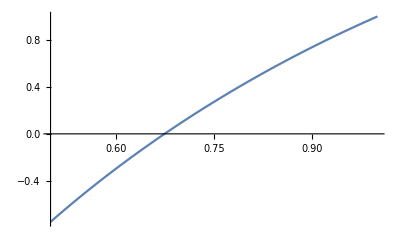

now = 0.590616 , 1 inc

now = 0.72845 , 2 inc

now = 0.647551 , 3 inc

now = 0.689965 , 4 inc

now = 0.666041 , 5 inc

now = 0.679061 , 6 inc

now = 0.671826 , 7 inc

now = 0.675802 , 8 inc

now = 0.673603 , 9 inc

now = 0.674815 , 10 inc

now = 0.674146 , 11 inc

```mathematica
(* Задание 4 *)

func4[x_] := Log[2, x] - x^2 + 3 * x - 1;
Plot[func4[x], {x, 0.5, 1}]

g[x_] :=func4'[x];
a= 0.5;
b=1;
If[Abs[g[a]]>Abs[g[b]],eps = g[a], eps=g[b]];
p[x_]:=x-(2/eps)*func4[x];
e=0.001;
i=0;
While[Abs[a-b]>e,
Increment[i];
a=b;
b=p[a];
Print["now = ", b, " , ", i, " inc"];
];
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

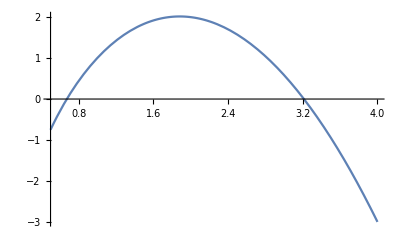

{x→0.674384}

{x→3.21285}

```mathematica
(* Задание 5 *)

func5[x_] = Log[2, x] - x^2 + 3 * x - 1;
Solve[func5[x] == 0];
NSolve[func5[x] == 0];
Plot[func5[x], {x, 0.5 , 4}]
FindRoot[func5[x] == 0, {x, 0.5}]
FindRoot[func5[x] == 0, {x, 3}]
```

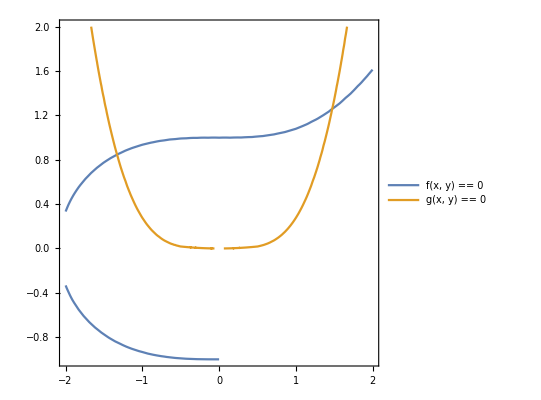

```mathematica
(* Задание 6 *)

fFunc[x_, y_] =  (x^3)/(7 - x) + 1 - y^2;
gFunc[x_, y_] = x^ 2  - 3 * ArcCos[1 - y/5];
ContourPlot[{fFunc[x,y] == 0, gFunc[x,y] == 0}, {x, -2, 2}, {y, -1, 2}, PlotLegends->{"f(x, y) == 0","g(x, y) == 0"}]
```

```mathematica
FindRoot[{fFunc[x,y]==0,gFunc[x,y]==0},{x,-1},{y,2}]
FindRoot[{fFunc[x,y]==0,gFunc[x,y]==0},{x,1},{y,2}]
```

{x→-1.331,y→0.84674}

{x→1.47468,y→1.25714}